```mathematica
Quit[]
```

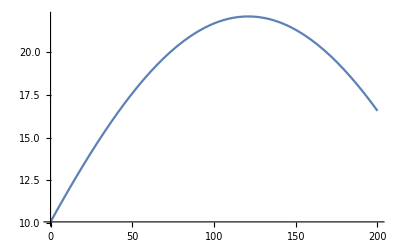

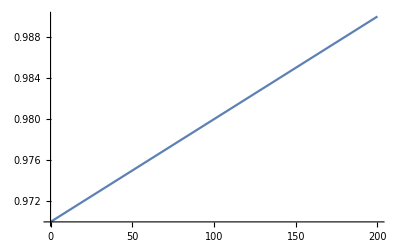

```mathematica
(*Temperature & water activity equation*)
T:= 4+18.09*Sin[0.01016*t+0.3418] (* equation for temperature (T) *)
Aw := 0.97+0.0001*t                                       (*equation for WaterActivity (Aw) *)
Plot[T,{t,0,200}]
Plot[Aw,{t,0,200}]
```

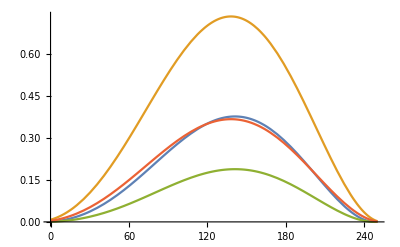

```mathematica
(* Growth equation for minimal temp and wateractivity*)
Growth = 2*((T-tmin)*(Aw-awmin))^2  ;  (*Growth for GMO near root*)
tmin=9;
awmin=0.95;
Growth2 = 2*((T-tmin2)*(Aw-awmin2))^2  ;(*Growth for WildType near root*)
tmin2=8;
awmin2=0.94;
Growth3 = ((T-tmin3)*(Aw-awmin3))^2 ; (*Growth for GMO in soil*)
tmin3=9;
awmin3=0.95;
Growth4 = ((T-tmin4)*(Aw-awmin4))^2 ;  (*Growth for wilddtype in soil*)
tmin4=8;
awmin4=0.94;
Plot[{Growth,Growth2,Growth3,Growth4},{t,0,250}] (*shows a plot of the growth factor over time*)
```

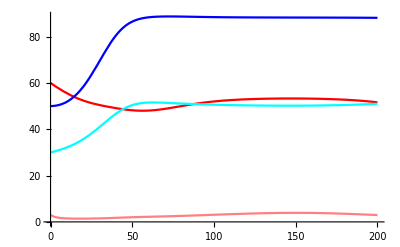

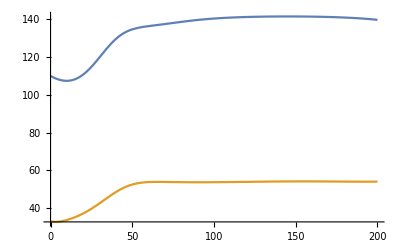

```mathematica
(*ODE Equation for our GMO*)
GMOplant = D[G[t],t] == Growth*G[t]*((Splant-G[t] -c*B[t])/Splant)+ToPlant-ToSoil    ;(* growth equation GMO near plant *)

GMOsoil= D[M[t],t] == (Growth3-0.5)*M[t]*((Ssoil-M[t]-c*A[t])/Ssoil)+ToSoil-ToPlant      ;  (* growth equation GMO Away from the plant*)
ToPlant:= M[t]* 0.001*((M[t]+c*A[t])/Ssoil)  ;  (*Patch tranfser from soil to plant (GMO)*)
ToSoil := G[t]*0.01*((G[t] +c*B[t])/Splant)     ;   (*patch transfer from plant to soil (GMO) *)


(*ODE equation for the wildtype baccilus*)
WildPlant= D[B[t],t]==Growth2*B[t]*((Splant-B[t]-d*G[t])/Splant) +ToPlant2-ToSoil2;(* growth equation Wildtype near plant *)

WildSoil= D[A[t],t]==Growth4* A[t]*((Ssoil- A[t]-d*M[t])/Ssoil)+ToSoil2-ToPlant2;(* growth equation Wildtype Away from the plant*)


ToPlant2 := A[t]* 0.01*((A[t]+d*M[t])/Ssoil);       (*Patch tranfser from soil to plant*)
ToSoil2:= B[t]*0.01*((B[t]+d*G[t])/Splant) ;    (*patch transfer from plant to soil *)

(*Parameters*)
Splant = 100;
Ssoil = 50;
S1 = 100; (*Max carrying capacity GMO near plant*)
S2 = 100;    (*Max carrying capacity Wildtype near plant*)
S3 = 75;    (*Max carrying capacity GMO away from plant*)
S4 = 75;    (*Max carrying capacity Wild Type away from plant*)
c = 0.5;   (* cempetitive influence of the Wildtype on the GMO*)
d = 0.21; (* competition coefficient of GMO on WIldtype *)

all = { GMOplant,GMOsoil, WildPlant,WildSoil};  (* system of ODEs*)
init = {G[0]==60,M[0]==3,B[0]==50,A[0]==30}; (* initial population density*)
Solution = NDSolveValue[{all,init},{G[t],M[t],B[t],A[t]},{t,0,200}];  (*solution for system of ODEs*)
Plot[Solution,{t,0,200},PlotStyle->{Red,Pink,Blue,Cyan}] 
Plot[{Solution[[1]]+Solution[[3]],Solution[[2]]+Solution[[4]]},{t,0,200}] 
(*plots the solution of the ODEs over time where red and pink are GMO and blue are the Wildtypes *)
```

```mathematica
Show[%163,ImageSize->Large]
```